```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters`
peeters`setGitDir["../project/figures/GAelectrodynamics"]
```

peeters`

/Users/pjoot/project/figures/GAelectrodynamics

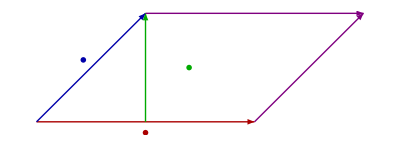

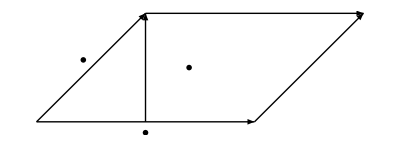

```mathematica
ClearAll[o, a, b, i, j, bb, bbi, c2v, bperp, bproj, brej,parallelogramAreaFig1, bwparallelogramAreaFig1, f]
o = {0,0};
a = {2,0};
b = {1,1};
bb = 1 + I;
i = {1,0};
j = {0,1};
bbi = bb * I;
c2v[z_] := {z//Re, z//Im}
bperp = (bbi // c2v )/Sqrt[2];
bproj = (b . a) a/((Norm[a])^2);
brej = b - bproj;


f[c1_, c2_, c3_, c4_] := Graphics[{
Thick,
c1,
Arrow[{o,a}], 
Text["\\mathbf{a}" //MaTeX, a/2 - 0.1j ],
c2,
Arrow[{o,b}],
Text["\\mathbf{b}" //MaTeX, b/2 +0.1 bperp ],
c3,
Arrow[{bproj, b}],
Text["(\\mathbf{b} \\wedge \\mathbf{a}) \\frac{1}{\\mathbf{a}}" //MaTeX, bproj + brej/2 + 0.4 i ],
c4,
Arrow[{a, a+ b}],
Arrow[{b,a+b}]
}]

parallelogramAreaFig1 = f[Red // Darker,Blue// Darker,Green // Darker,Purple]
bwparallelogramAreaFig1 = f[Black, Black, Black, Black]
```

```mathematica
(*https://stackoverflow.com/questions/4641512/how-to-install-new-packages-for-mathematica*)
```

```mathematica
$UserBaseDirectory
```

/Users/pjoot/Library/Mathematica

```mathematica
peeters`exportForLatex["color/parallelogramAreaFig1",parallelogramAreaFig1]
peeters`exportForLatex["bw/parallelogramAreaFig1",bwparallelogramAreaFig1]
```

{color/parallelogramAreaFig1.eps,color/parallelogramAreaFig1pn.png}

{bw/parallelogramAreaFig1.eps,bw/parallelogramAreaFig1pn.png}